Multi-Control Unitary Gates |

Definitionpaclet:Q3/tutorial/MultiControlUnitaryGates#821655741 | Multi-Control NOT Gatepaclet:Q3/tutorial/MultiControlUnitaryGates#990819799
Gray-Code Methodpaclet:Q3/tutorial/MultiControlUnitaryGates#46593121 |

See also Section 2.3 of the Quantum Workbook (Springer, 2022)https://doi.org/10.1007/978-3-030-91214-7.

A multi-control unitary gate is a generalization of a controlled-unitary gate, where the single control qubit is replaced by a register of multiple qubits. The unitary gate on the target qubit (or register in general) takes effects only when every qubit in the control register is set to state |1⟩.

Multi-control unitary gates comprise the vital part of decomposing arbitrary multi-qubit unitary gates into elementary gates. Moreover, reliable implementation of multi-control unitary gates is essential in many quantum algorithms. Notable examples are quantum decision problems and quantum search problems.

ControlledUpaclet:Q3/ref/ControlledUQ3 Package Symbol | Represents a multi-control multi-target unitary gate
TwoLevelDecompositionpaclet:Q3/ref/TwoLevelDecompositionQ3 Package Symbol | Decomposes an arbitrary unitary gate into two-level unitary transformations
TwoLevelUpaclet:Q3/ref/TwoLevelUQ3 Package Symbol | Represents a two-level unitary matrix
Toffolipaclet:Q3/ref/ToffoliQ3 Package Symbol | The Toffoli gate
Fredkinpaclet:Q3/ref/FredkinQ3 Package Symbol | The Fredkin gate
Deutschpaclet:Q3/ref/DeutschQ3 Package Symbol | The Deutsch gate

Q3 functions related to multi-control unitary gates.

Make sure that the Q3 package is loaded to use the demonstrations in this documentation.

```mathematica
<<Q3`
```

Throughout this document, symbol S will be used to denote qubits and Pauli operators on them. Similarly, symbol c will be used to denote complex-valued coefficients.

```mathematica
Let[Qubit,S]
Let[Complex,c]
```

Definition

Let 𝒮^(⊗m) and 𝒮^(⊗n) be the Hilbert spaces of the control and target register consisting of m and n qubits, respectively. Suppose that U is a unitary operator on the target register. The multi-control unitary operator is defined by

c⊗t↦c⊗(U^(c_1 c_2(⋯c)_m)t) ,

where c≡(c_1 c_2 . . . c_m)_2. The unitary transformation U acts on the target qubits only when every qubit in the control register is set to |1⟩.

We will be most interested in the case with n = 1, where the matrix representation takes the form

(1 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0
0 | 0 | ⋱ | ⋮ | ⋮
0 | 0 | ⋯ | U_11 | U_12
0 | 0 | ⋯ | U_21 | U_22) .

The above is a prototype form of a two-level unitary matrix on multiple qubits. Indeed, any two-level unitary matrix can be put into this form by exchanging columns and rows—equivalent to basis changes. The multi-control unitary gates thus arise naturally as we discuss the universal quantum computation.

In the quantum circuit model, a multi-control unitary gate is represented as

```mathematica
QuantumCircuit[ControlledU[S@{1,2,3},S[4,1],"Label"->"U"]]
```

-Graphics-

Gray-Code Method

We discuss one systematic method based on the Gray code to decompose a multi- control unitary gate into factors of either the single-qubit controlled-unitary or CNOT gate. For example, consider a 3-control unitary gate as shown in the following quantum circuit (Barenco et al., 1995)

=-Graphics-

where V is another unitary operator such that V^4=U. When every control qubit is set to |1⟩, all V gates in the diagram take effects on the target qubit while the V^† gates are ineffective. To examine the case with the control qubits in a general state x_1⊗x_2⊗⋯⊗x_n, note that the gates on the target qubit are effective under the conditions specified in terms of the bit values at the bottom of the above diagram. The conditions are systematically fulfilled by following the Gray code sequence, an arrange of bits such that two successive values differ in only one bit, the bit strings of which are indicated at the top of the diagram. The identity for the bitwise AND,

2^(n-1)(x_1 x_2(⋯x)_n)=∑_k_1 x_k_1-∑_(k_1<k_2) (x_k_1⊕x_k_2)+∑_(k_1<k_2<k_3) (x_k_1⊕x_k_2⊕x_k_3)-⋯+(-1)^(n-1)(x_1⊕x_2⊕⋯⊕x_n) ,

ensures that the above quantum circuit on the right-hand side reproduces the desired multi-control unitary gate on the left-hand side.

In general, an n-control unitary gate can be implemented by combining 2^(n-1) controlled-V gates, (2^(n-1)-1) controlled-V^† gates, and (2^n-2) CNOT gates, where V is a unitary operator satisfying V^(2^(n-1))=U. For a relatively small n (n≤8), the Gray-code method is known to be the most efficient method. However, it grows exponentially and eventually becomes impractical. For such cases, several alternative methods have been proposed where the computational cost increases quadratically with the size of the control register (Barenco et al., 1995; Nielsen & Chuang, 2011).

### Example

Let us consider a 3-control unitary gate.

```mathematica
$L=3;
jj=Range[$L];
cc=S[jj,None];
```

This is the gate to operate on the target qubit.

```mathematica
T=S[$L+1,None];
op=Rotation[Pi/3,T[1]]//Elaborate
```

(√3)/2-(ⅈ S_4^x)/2

This decomposes the multi-control unitary gate based on the Gray code -- showing only a part of it. Each component is either CNOT or a two-qubit-control unitary gate.

```mathematica
gc=GrayControlledU[cc,op]; gc[[;;3]]
```

{ControlledU[{S_1},(2^(1/4) ⅇ^(-(ⅈ π)/24)+2^(1/4) ⅇ^((ⅈ π)/24))/(2 2^(1/4))+((2^(1/4) ⅇ^(-(ⅈ π)/24)-2^(1/4) ⅇ^((ⅈ π)/24)) S_4^+)/(2 2^(1/4))+((2^(1/4) ⅇ^(-(ⅈ π)/24)-2^(1/4) ⅇ^((ⅈ π)/24)) S_4^-)/(2 2^(1/4)),Label→V],CNOT[{S_1},{S_2}],ControlledU[{S_2},(2^(1/4) ⅇ^(-(ⅈ π)/24)+2^(1/4) ⅇ^((ⅈ π)/24))/(2 2^(1/4))+((-2^(1/4) ⅇ^(-(ⅈ π)/24)+2^(1/4) ⅇ^((ⅈ π)/24)) S_4^+)/(2 2^(1/4))+((-2^(1/4) ⅇ^(-(ⅈ π)/24)+2^(1/4) ⅇ^((ⅈ π)/24)) S_4^-)/(2 2^(1/4)),Label→V^†]}

This is a quantum circuit model of the decomposition.

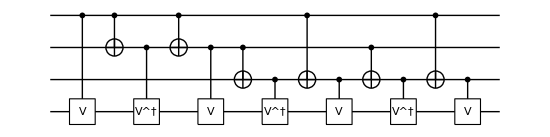

```mathematica
qc=QuantumCircuit@@gc
```

Finally, check the result.

```mathematica
expr=ExpressionFor[qc];
expr2=ControlledU[cc,op]//Elaborate;
expr-expr2//Simplify
```

0

Multi-Control NOT Gate

The multi-control NOT gate is an important special case of the multi-control unitary gate, where the unitary operator U equals to the Pauli X operator. It transforms the logical basis states as

c⊗t↦c⊗(X^(c_1 c_2(⋯c)_m)t) ,

or equivalently,

c⊗t↦c⊗(c_1 c_2(⋯c)_m)⊕t .

The multi-control NOT gate commonly occurs when one converts the two-level unitary transformation on more than two qubits.

For demonstration, consider a 4-control NOT gate.

```mathematica
qc=QuantumCircuit[CNOT[S@{1,2,3},S[4]]]
```

-Graphics-

Here is the explicit expression of the multi-control NOT gate in terms of the Pauli operators.

```mathematica
op=ExpressionFor[qc]
```

7/8-1/8 S_1^z S_2^z-1/8 S_1^z S_3^z-1/8 S_1^z S_4^x-1/8 S_2^z S_3^z-1/8 S_2^z S_4^x-1/8 S_3^z S_4^x+1/8 S_1^z S_2^z S_3^z+1/8 S_1^z S_2^z S_4^x+1/8 S_1^z S_3^z S_4^x+1/8 S_2^z S_3^z S_4^x-1/8 S_1^z S_2^z S_3^z S_4^x+S_1^z/8+S_2^z/8+S_3^z/8+S_4^x/8

Here we compare it with the expression explicitly constructed in terms of a projection operator.

```mathematica
prj=Multiply@@S[{1,2,3},11];
new=(1-prj)+prj**S[4,1]//Elaborate
```

7/8-1/8 S_1^z S_2^z-1/8 S_1^z S_3^z-1/8 S_1^z S_4^x-1/8 S_2^z S_3^z-1/8 S_2^z S_4^x-1/8 S_3^z S_4^x+1/8 S_1^z S_2^z S_3^z+1/8 S_1^z S_2^z S_4^x+1/8 S_1^z S_3^z S_4^x+1/8 S_2^z S_3^z S_4^x-1/8 S_1^z S_2^z S_3^z S_4^x+S_1^z/8+S_2^z/8+S_3^z/8+S_4^x/8

```mathematica
op-new//Elaborate
```

0

An efficient implementation of a multi-control NOT gate uses additional qubits not directly involved in the gate operation itself as in the following quantum circuit (Barenco et al., 1995):

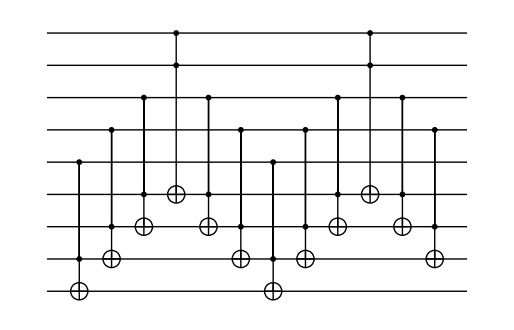
=-Graphics-

It is emphasized that the quantum states of the extra qubits should not be confused with the so-called “ancillary qubits” in the sense that they do not have to be initialized in a certain fixed quantum state and their state is not altered. The desired gate operation is performed properly regardless of the initial state of the extra qubits and their quantum state is restored after the gate operation.

For demonstration, consider a 4-control NOT gate.

```mathematica
$n=4;
$m=2;
cc=Range[$n];
aa=Range[$n+1,$n+$m];
tt=$n+$m+1;
```

```mathematica
qc=QuantumCircuit[CNOT[S[cc],S[tt]],"Visible"->S[aa]]
```

-Graphics-

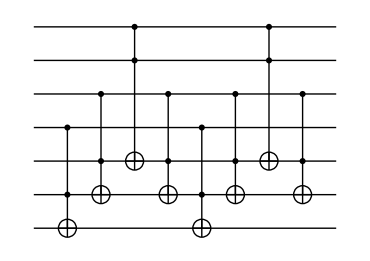

```mathematica
tofa=Table[Toffoli[S[$n-j+1],S[$n+$m-j+1],S[tt-j+1]],{j,1,$m}];
tofb=Toffoli[S[1],S[2],S[$n+1]];
tofc=Rest@tofa;
new=QuantumCircuit[Sequence@@Flatten@{tofa,tofb,Reverse@tofa,tofc,tofb,Reverse@tofc}]
```

```mathematica
Timing[Elaborate[qc-new]]
```

{6.36305,0}

### Toffoli Gate

In the above, we have introduced the Toffoli gate, a 2-control NOT gate.  The Toffoli gate has attracted interest because it is universal for classical reversible computation. Unfortunately, however, it is not universal for quantum computation.

Let us analyze the Toffoli gate a bit further.

```mathematica
qc=QuantumCircuit[Toffoli[S[1],S[2],S[3]]]
```

-Graphics-

Here is the explicit expression in terms of the Pauli operators.

```mathematica
toff=ExpressionFor[qc]
```

3/4-1/4 S_1^z S_2^z-1/4 S_1^z S_3^x-1/4 S_2^z S_3^x+1/4 S_1^z S_2^z S_3^x+S_1^z/4+S_2^z/4+S_3^x/4

It can be implemented by a combination of two-qubit gates.

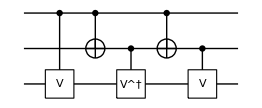

3/4-1/4 S_1^z S_2^z-1/4 S_1^z S_3^x-1/4 S_2^z S_3^x+1/4 S_1^z S_2^z S_3^x+S_1^z/4+S_2^z/4+S_3^x/4

0

```mathematica
gray=GrayControlledU[S@{1,2},S[3,1]];
qc=QuantumCircuit[Sequence@@gray]
expr=ExpressionFor[qc]
toff-expr
```

Here V=√X, and its matrix representation looks like this.

```mathematica
matV=MatrixPower[ThePauli[1],1/2];
matV*2/(1+I)//MatrixForm
opV=Elaborate@ExpressionFor[matV,S[3]]
```

(1 | -ⅈ
-ⅈ | 1)

(1/2+ⅈ/2)+(1/2-ⅈ/2) S_3^x

Reversing the above circuit gives the identical result.

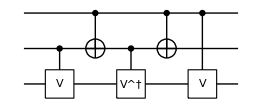

3/4-1/4 S_1^z S_2^z-1/4 S_1^z S_3^x-1/4 S_2^z S_3^x+1/4 S_1^z S_2^z S_3^x+S_1^z/4+S_2^z/4+S_3^x/4

0

```mathematica
qc=QuantumCircuit@@Reverse@gray
expr=ExpressionFor[qc]
toff-expr
```

As noted by Smolin & DiVincenzo (1996), it can also be reordered as follows, and this rearrangement is useful in optimizing the Fredkin gate, another universal gate for classical reversible computation.

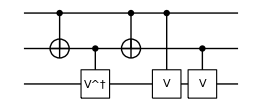

3/4-1/4 S_1^z S_2^z-1/4 S_1^z S_3^x-1/4 S_2^z S_3^x+1/4 S_1^z S_2^z S_3^x+S_1^z/4+S_2^z/4+S_3^x/4

0

```mathematica
qc=QuantumCircuit@@Permute[gray,Cycles[{{4,3,2,1}}]]
expr=ExpressionFor[qc]
toff-expr
```

### Fredkin Gate

The Fredkin gate “swaps” the states of the two target qubits when the control qubit is set in the state |1⟩, as depicted by the following two equivalent quantum circuit elements

```mathematica
qc=QuantumCircuit[Fredkin[S[1],S[2],S[3]]]
```

-Graphics-

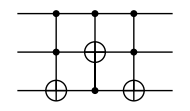

```mathematica
new=QuantumCircuit[CNOT[S@{1,2},S[3]],CNOT[S@{1,3},S[2]],CNOT[S@{1,2},S[3]]]
```

```mathematica
qc-new//Elaborate
```

0

In fact, the relation between the SWAP gate and the CNOT gate suggests that there is another equivalent quantum circuit of the Fredkin gate,

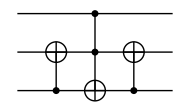

```mathematica
sml=QuantumCircuit[CNOT[S[3],S[2]],CNOT[S@{1,2},S[3]],CNOT[S[3],S[2]]]
```

```mathematica
qc-sml//Elaborate
```

0

which is simpler than the one given above. This equivalent quantum circuit was used by Smolin & DiVincenzo (1996) for an efficient implementation of the Fredkin gate in terms of the elementary gates. Like the Toffoli gate, the Fredkin gate is not universal for quantum computation.

| Related Guides
▪Quantum Computation and Quantum Information

| Related Tutorials
▪Quantum Computation: Overview
▪Quantum Computation and Quantum Information with Q3

| Related Links
▪A. Barenco, https://doi.org/10.1103/physreva.52.3457et al., Physical Review A 52 (5), 3457 (1995)https://doi.org/10.1103/physreva.52.3457, "Elementary gates for quantum computation."
▪J. A. Smolin and D. P. DiVincenzo, Physical Review A 53 (4), 2855 (1996)https://doi.org/10.1103/PhysRevA.53.2855, "Five two-bit quantum gates are sufficient to implement the quantum Fredkin gate." 
▪M. Nielsen and I. L. Chuang, Quantum Computation and Quantum Information (Cambridge University Press, New York, 2011)https://doi.org/10.1017/CBO9780511976667.
▪Mahn-Soo Choi, A Quantum Computation Workbook (Springer, 2021)https://doi.org/10.1007/978-3-030-91214-7.